```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
datafull=Import["../data/CGL_num.csv",HeaderLines->2];
datafull[[1]]
Dimensions@datafull
```

{3616,4,280110,17130421-02000,7,26,0,680,750,750,700,462.778,144.207,144.207,0.3,1044,1.92,2004.48,24.008,1525.99,152.861,154.39,0.542195,207037,0.300134,0,29-DEC-17 01.22.39.000000000 PM -06:00}

{44963,27}

```mathematica
nullpos=Position[datafull[[All,17]],_?(Head@#==String&)];
datafull=Delete[datafull,nullpos];
```

```mathematica
(* mostlyzeropos=Position[datafull[[All,9]],_?(#==0&)][[{2,3}]];
datafull=Delete[datafull,mostlyzeropos]; *)
```

```mathematica
deletepos=Position[datafull[[All,17]],_?(1200<#&)];
datafull=Delete[datafull,deletepos];
```

```mathematica
deletepos2=Position[datafull[[All,16]],_?(80000<#&)];
datafull=Delete[datafull,deletepos2];
```

```mathematica
deletepos3=Position[datafull[[All,16]],_?(200>#&)];
datafull=Delete[datafull,deletepos3];
```

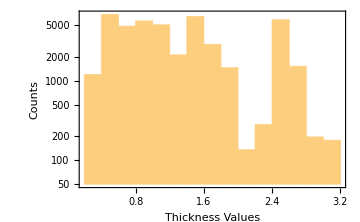
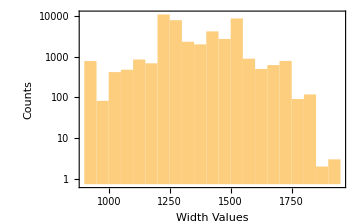

```mathematica
{Histogram[datafull[[All,17]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,16]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
density[thick_,width_,length_,weight_]:=N@weight/(thick*width*length);
```

```mathematica
thickvaluesthkpos=datafull[[All,17]];
widthvaluesthkpos=datafull[[All,16]];
lengthvaluesthkpos=datafull[[All,20]];
weightvaluesthkpos=datafull[[All,19]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
KeySort@Counts@densities
```

<|-0.00686112→1,-0.00463997→1,-0.00209751→1,-0.00135243→1,-0.000638687→1,43602,0.00164515→1,0.00205702→1,0.00218787→1,0.00246979→1,0.00249878→1|>
 |  |  |  |

```mathematica
datafull=datafull[[Flatten@Position[densities,_?(6.5*10^(-6)<#<8.5*10^(-6)&)]]];
```

```mathematica
datafull=Delete[datafull,Position[datafull[[All,27]],_?(#==""&)]];
```

```mathematica
thickvaluesthkpos=datafull[[All,17]];
widthvaluesthkpos=datafull[[All,16]];
lengthvaluesthkpos=datafull[[All,20]];
weightvaluesthkpos=datafull[[All,19]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
```

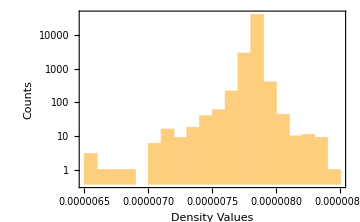

```mathematica
Histogram[densities,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Density Values","Counts"},ImageSize->Medium]
```

```mathematica
Length@datafull
```

44711

```mathematica
timecolumn=Table[{StringDrop[datafull[[i,27]],-7],Which[StringDrop[datafull[[i,27]],{1,32}]=="-06:00",-4,StringDrop[datafull[[i,27]],{1,32}]=="-05:00",-3]},{i,Length@datafull}]
```

{{29-DEC-17 01.22.39.000000000 PM,-4},{29-DEC-17 01.38.09.000000000 PM,-4},{29-DEC-17 01.50.48.000000000 PM,-4},44705,{02-NOV-20 07.03.32.000000000 AM,-4},{02-NOV-20 07.19.39.000000000 AM,-4},{02-NOV-20 07.34.19.000000000 AM,-4}}
 |  |  |  |

```mathematica
timecolumnconvert=Table[TimeZoneConvert[DateObject[StringReplacePart[i[[1]],":",{{13,13},{16,16}}],TimeZone->i[[2]]],$TimeZone],{i,timecolumn}]
```

{Fri 29 Dec 2017 19:22:39GMT+2,Fri 29 Dec 2017 19:38:09GMT+2,Fri 29 Dec 2017 19:50:48GMT+2,Sat 30 Dec 2017 00:08:02GMT+2,44704,Mon 2 Nov 2020 13:03:32GMT+2,Mon 2 Nov 2020 13:19:39GMT+2,Mon 2 Nov 2020 13:34:19GMT+2}
 |  |  |  |

```mathematica
timecolumnseconds=Table[AbsoluteTime@i,{i,timecolumnconvert}]
```

{3723564159,3723565089,3723565848,3723581282,3723582508,3723583636,3723584720,3723585812,3723586896,3723587988,3723589059,3723590138,44687,3813300701,3813301701,3813302824,3813303932,3813305046,3813307201,3813308278,3813309160,3813310095,3813311012,3813311979,3813312859}
 |  |  |  |

```mathematica
datafull=Join[datafull,Partition[timecolumnseconds,1],2];
Dimensions@datafull
```

{44711,28}

```mathematica
datafull[[1]]
```

{3616,4,280110,17130421-02000,7,26,0,680,750,750,700,462.778,144.207,144.207,0.3,1044,1.92,2004.48,24.008,1525.99,152.861,154.39,0.542195,207037,0.300134,0,29-DEC-17 01.22.39.000000000 PM -06:00,3723564159}

```mathematica
datafullsorted=Sort[datafull,#1[[1]]<#2[[1]]&];
```

```mathematica
Dimensions@datafullsorted
```

{44711,28}

Deletion of sequences less than 50

```mathematica
deletepos4=Flatten@Table[Position[datafullsorted[[All,1]],i],{i,Keys@Cases[Normal@Counts@datafullsorted[[All,1]],_?(Values[#]<50&)]}];
datafullsorted=Delete[datafullsorted,Partition[deletepos4,1]];
```

```mathematica
datafullsorted[[1]]
```

{3712,8,326753,17177641-01000,8,30,0.7,660,710,710,670,462.778,144.207,144.207,0.5,1221,0.88,1074.48,20.654,2448.7,149.539,150.282,0.701007,207298,0.498408,1,11-JAN-18 06.31.40.000000000 PM -06:00,3724705900}

```mathematica
programids=DeleteDuplicates@datafullsorted[[All,1]];
Length@programids
datafullsortedfinal=Flatten[Table[Sort[Select[datafullsorted,#[[1]]==i&],#1[[28]]<#2[[28]]&],{i,programids}],1];
Dimensions@datafullsortedfinal
```

453

{31230,28}

```mathematica
datafullsortedfinal[[1]]
```

{3712,8,323371,17173001-02000,8,26,0.7,680,750,750,700,462.778,144.207,144.207,0.5,951,0.49,465.99,15.688,4289.31,154.085,153.164,0.50032,207298,0.498736,0,10-JAN-18 07.28.57.000000000 AM -06:00,3724579737}

```mathematica
datafullsortedfinal[[2,{3,4}]]
```

{323382,17173021-03000}

```mathematica
pltcmdata=Import["../data/pltcm_manipulated_59604_rev1.csv",HeaderLines->2];
(*pltcmdata=Import["../data/PLTCM_num.csv",HeaderLines->2];*)
```

```mathematica
Dimensions@pltcmdata
Dimensions@datafullsortedfinal
```

{59602,22}

{31230,28}

```mathematica
int=Intersection[pltcmdata[[All,{21,22}]],datafullsortedfinal[[All,{3,4}]]];
Dimensions@int
```

{27147,2}

```mathematica
(*pltcmpos=Position[pltcmdata[[All,21]],Alternatives@@int];
cglpos=Position[datafullsortedfinal[[All,3]],Alternatives@@int];
Dimensions@pltcmpos
Dimensions@cglpos*)
```

{0}

{0}

```mathematica
pltcmpos2=Flatten[Position[pltcmdata[[All,{21,22}]],#],1]&/@int;
cglpos2=Flatten[Position[datafullsortedfinal[[All,{3,4}]],#],1]&/@int;
```

```mathematica
Length@pltcmpos2
Length@Flatten@pltcmpos2
Length@cglpos2
Length@Flatten@cglpos2
```

27147

27456

27147

27395

```mathematica
pospospltcm=Flatten@Position[Table[Length@i,{i,pltcmpos2}],_?(#≠1&)];
pltcmpos3=Flatten@Join[pltcmpos2[[Complement[Range@Length@pltcmpos2,pospospltcm]]],Table[pltcmpos2[[i]][[1]],{i,pospospltcm}]];
```

```mathematica
posposcgl=Flatten@Position[Table[Length@i,{i,cglpos2}],_?(#≠1&)];
cglpos3=Flatten@Join[cglpos2[[Complement[Range@Length@cglpos2,posposcgl]]],Table[cglpos2[[i]][[1]],{i,posposcgl}]];
```

```mathematica
pltcmdata[[pltcmpos3,{18,20,21,22}]]
datafullsortedfinal[[cglpos3,All]]
```

{{1.86231,1262.07,296815,17143301-01000},{1.30207,1496.21,320386,17170801-01000},{1.3007,1487.21,322849,17173721-01000},{0.759561,1166.76,323340,17172921-01000},{0.614603,1073.49,323350,17172941-05000},{0.614111,1073.49,323351,17172941-06000},{0.614574,1073.49,323352,17172941-07000},27134,{0.911862,1235.83,1037870,20101961-04000},{0.891542,1506.54,1045749,20110141-05000},{0.48,1452.2,1047799,20111681-01000},{1.17975,1121.24,1075113,20136821-07000},{1.8,1228.92,1083822,20141641-01000},{0.904616,1233.79,1100661,20152421-06000}}
 |  |  |  |

{{4515,7,296815,17143301-01000,8,26,0,680,750,750,700,463,96.2172,96.2172,0.7,1261,1.8821,2373.33,25.018,1343.05,96.4868,97.757,0,208696,0.692081,1,18-MAR-18 06.01.06.000000000 AM -05:00,3730359666},27145,{22446,7,1110069,20161001-01000,8,26,0.7,680,750,750,700,463,48.0894,48.0894,0.5,1520.59,0.4104,624.049,20.132,4116.37,46.9788,49.5342,0.6999,236084,0.5009,0,25-OCT-20 02.51.27.000000000 AM -05:00,3812601087}}
 |  |  |  |

```mathematica
Sort@datafullsortedfinal[[cglpos3,3]]==Sort@pltcmdata[[pltcmpos3,21]]
```

True

```mathematica
Sort[datafullsortedfinal[[cglpos3,All]],#1[[3]]<#2[[3]]&];
```

```mathematica
Sort[pltcmdata[[pltcmpos3,{18,20,21,22}]],#1[[3]]<#2[[3]]&];
```

```mathematica
%487[[All,4]]==%488[[All,4]]
```

True

```mathematica
Table[%487[[i,4]]==%488[[i,4]],{i,27147}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,27019,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}
 |  |  |  |

```mathematica
Counts@%494
```

<|True→27147|>

```mathematica
datafullsortedfinal[[Flatten@Position[datafullsortedfinal[[All,{3,4}]],cglpltcmintersect[[2500]]],{17,16}]]
pltcmdata[[Flatten@Position[pltcmdata[[All,{21,22}]],cglpltcmintersect[[2500]]],{18,20}]]
```

{{1.4367,1264}}

{{1.40808,1264.61}}

```mathematica
part1=Sort[datafullsortedfinal[[cglpos3,All]],#1[[3]]<#2[[3]]&];
Dimensions@part1
part2=Sort[pltcmdata[[pltcmpos3,{18,20,21,22}]],#1[[3]]<#2[[3]]&];
Dimensions@part2
```

{27147,28}

{27147,4}

```mathematica
datafullcombined=Join[part1,part2[[All,{1,2}]],2]
Dimensions@datafullcombined
```

{{4515,7,296815,17143301-01000,8,26,0,680,750,750,700,463,96.2172,96.2172,0.7,1261,1.8821,2373.33,25.018,1343.05,96.4868,97.757,0,208696,0.692081,1,18-MAR-18 06.01.06.000000000 AM -05:00,3730359666,1.86231,1262.07},27145,{22797,4,1116719,20165761-05000,8,26,0.7,680,750,750,700,463,96.2172,96.2172,0.5,1419.73,0.594279,843.716,20.92,3165.1,97.0177,92.8563,0.695946,236084,0.301396,1,01-NOV-20 01.35.02.000000000 PM -06:00,3813248102,0.580701,1420.53}}
 |  |  |  |

{27147,30}

```mathematica
datafullcombinedsorted=Sort[datafullcombined,#1[[1]]<#2[[1]]&];
```

```mathematica
programids=Sort@DeleteDuplicates@datafullcombinedsorted[[All,1]];
```

```mathematica
datafullcombinedsortedfinal=Flatten[Table[Sort[Select[datafullcombinedsorted,#[[1]]==i&],#1[[28]]<#2[[28]]&],{i,programids}],1];
```

```mathematica
datafullcombinedsortedfinal[[{1,2,3,4}]]
```

{{3712,8,323371,17173001-02000,8,26,0.7,680,750,750,700,462.778,144.207,144.207,0.5,951,0.49,465.99,15.688,4289.31,154.085,153.164,0.50032,207298,0.498736,0,10-JAN-18 07.28.57.000000000 AM -06:00,3724579737,0.485686,950.073},{3712,8,323382,17173021-03000,8,26,0.7,680,750,750,700,462.778,144.207,144.207,0.5,950,0.51,484.5,15.886,4177.51,155.984,155.933,0.499851,207298,0.499338,0,10-JAN-18 07.59.01.000000000 AM -06:00,3724581541,0.48593,950.073},{3712,8,323374,17173001-05000,8,26,0.7,680,750,750,700,462.778,144.207,144.207,0.5,950,0.5,475,15.84,4248.72,156.311,157.843,0.500153,207298,0.499263,0,10-JAN-18 08.29.00.000000000 AM -06:00,3724583340,0.485982,950.073},{3712,8,323380,17173021-01000,8,26,0.7,680,750,750,700,462.778,144.207,144.207,0.5,951,0.52,494.52,15.847,4083,156.794,155.487,0.499984,207298,0.499009,0,10-JAN-18 08.58.55.000000000 AM -06:00,3724585135,0.486016,950.073}}

```mathematica
data=Join[Partition[Range@Length@datafullcombinedsortedfinal,1],datafullcombinedsortedfinal[[All,{1}]],ConstantArray[{0},Length@datafullcombinedsortedfinal],datafullcombinedsortedfinal[[All,{6,16,17,19,20,30,29,27,28}]],2]
```

{{1,3712,0,26,951,0.49,15.688,4289.31,950.073,0.485686,10-JAN-18 07.28.57.000000000 AM -06:00,3724579737},{2,3712,0,26,950,0.51,15.886,4177.51,950.073,0.48593,10-JAN-18 07.59.01.000000000 AM -06:00,3724581541},{3,3712,0,26,950,0.5,15.84,4248.72,950.073,0.485982,10-JAN-18 08.29.00.000000000 AM -06:00,3724583340},27142,{27146,22797,0,26,1438.77,0.763026,21.02,2437.07,1439.53,0.749486,02-NOV-20 07.19.39.000000000 AM -06:00,3813311979},{27147,22797,0,26,1426.07,0.736646,18.34,2218.18,1426.83,0.72873,02-NOV-20 07.34.19.000000000 AM -06:00,3813312859}}
 |  |  |  |

```mathematica
Dimensions@data
```

{27147,12}

```mathematica
(* Export["cgl_manipulated_31230.csv",data] *)
```

```mathematica
Export["../data/cgl_manipulated_27147_rev1.csv",data]
```

../data/cgl_manipulated_27147_rev1.csv